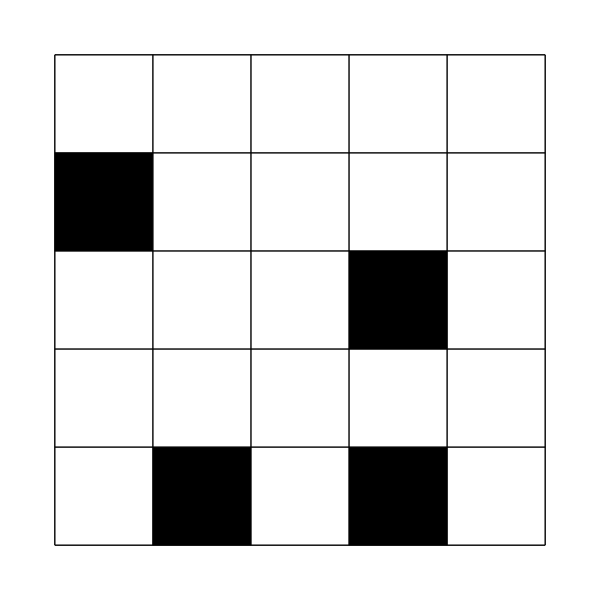
-Graphics-   -Graphics-

-Graphics-   -Graphics-

```mathematica
dir={{1,0},{-1,0},{0,1},{0,-1},{1,1},{-1,-1},{-1,1},{1,-1}};
```

```mathematica
n=4;
```

```mathematica
lenpath[path_]:=Module[{t,n},
If[Length[path]==1,Return[0]];
t=Reverse[RotateRight[path]-path];
n=1;
While[Length[t]>1&&t[[1]]==t[[2]],While[t[[1]]==t[[2]],t=Rest[t];n++]];n]
```

```mathematica
cont[path_,otherpath_,blocks_]:=Module[{last,s,i,temp,a,j,k,t,allowed},
last=Last[path];
allowed=dir;
If[Length[path]>1,allowed=Select[allowed,#=!=path[[-1]]-path[[-2]]&]];
s={};
For[i=1,i≤Length[allowed],i++,
a=allowed[[i]];
j=1;
While[t=last+j a;1≤t[[1]]≤n&&1≤t[[2]]≤n&&Not[MemberQ[path~Join~Drop[otherpath,-1]~Join~blocks,t]],AppendTo[s,Table[last+k a,{k,1,j}]];j++]];s]
```

```mathematica
initpic[s_]:=Style[Graphics[{
Table[Line[{{0,i},{n,i}}],{i,0,n}],
Table[Line[{{i,0},{i,n}}],{i,0,n}],
Map[Rectangle[#-1,#]&,blocks],
Text[Style["S",FontSize->18],s[[1]]-{.5,.55}],Text[Style["F",FontSize->18],s[[-1]]-{.5,.55}]
},ImageSize->20n],Antialiasing->False]
```

```mathematica
pic[s_]:=Style[Graphics[{
Table[Line[{{0,i},{n,i}}],{i,0,n}],
Table[Line[{{i,0},{i,n}}],{i,0,n}],
Map[Rectangle[#-1,#]&,blocks],
Red,AbsoluteThickness[2],Line[Map[#-{1/2,1/2}&,s]],Black,Text[Style["S",FontSize->18],s[[1]]-{.5,.55}],Text[Style["F",FontSize->18],s[[-1]]-{.5,.55}]
},ImageSize->20n],Antialiasing->False]
```

```mathematica
n=5; (*start and end in corners *)
doneblocks={};
For[k=1,k>0,k++,blocks=Union[Table[{RandomInteger[{1,n}],RandomInteger[{1,n}]},{RandomInteger[{4,4}]}]];
While[Length[Intersection[blocks,{{1,1},{n,n}}]]>0||MemberQ[doneblocks,blocks],blocks=Union[Table[{RandomInteger[{1,n}],RandomInteger[{1,n}]},{RandomInteger[{4,4}]}]]]
stac={{{{1,1}},{{n,n}},0}};
solns={};
While[Length[stac]>0&&Length[solns]<2,
cur=First[stac];
stac=Rest[stac];
path=cur[[1]];
otherpath=cur[[2]];
status=cur[[3]];
If[status==1&&Last[path]==Last[otherpath]&&Length[path]+Length[otherpath]+Length[blocks]==n^2+1&&path[[-1]]-path[[-2]]=!=otherpath[[-2]]-otherpath[[-1]],AppendTo[solns,Join[path,Drop[Reverse[otherpath],1]]]];
If[status==0&&Last[path]==Last[otherpath]&&Length[path]+Length[otherpath]+Length[blocks]==n^2+1&&lenpath[path]==lenpath[otherpath]&&path[[-1]]-path[[-2]]=!=otherpath[[-2]]-otherpath[[-1]],AppendTo[solns,Join[path,Drop[Reverse[otherpath],1]]]];
If[Intersection[path,otherpath]=={},
c=Map[Join[path,#]&,cont[path,otherpath,blocks]];
If[status==1,c=Select[c,lenpath[#]==lenpath[otherpath]&]];
poss=Map[{otherpath,#,1-status}&,c];
stac=Join[poss,stac]]];
(*Print[Length[blocks],"  ",Length[solns]];*)
If[Length[solns]==1,AppendTo[doneblocks,blocks];Print[initpic[{}],"   ",pic[solns[[1]]]]]]
```

```mathematica
n=6;
minblocks=8;
maxblocks=10;
doneblocks={};
For[k=1,k>0,k++,
start={RandomInteger[{1,4}],RandomInteger[{1,4}]};
end={RandomInteger[{1,4}],RandomInteger[{1,4}]};
While[start==end,end={RandomInteger[{1,4}],RandomInteger[{1,4}]}];
blocks=Union[Table[{RandomInteger[{1,n}],RandomInteger[{1,n}]},{RandomInteger[{minblocks,maxblocks}]}]];
While[Length[Intersection[blocks,{start,end}]]>0||MemberQ[doneblocks,blocks],blocks=Union[Table[{RandomInteger[{1,n}],RandomInteger[{1,n}]},{RandomInteger[{minblocks,maxblocks}]}]]];
stac={{{start},{end},0}};
solns={};
While[Length[stac]>0&&Length[solns]<2,
cur=First[stac];
stac=Rest[stac];
path=cur[[1]];
otherpath=cur[[2]];
status=cur[[3]];
If[status==1&&Last[path]==Last[otherpath]&&Length[path]+Length[otherpath]+Length[blocks]==n^2+1&&path[[-1]]-path[[-2]]=!=otherpath[[-2]]-otherpath[[-1]],AppendTo[solns,Join[path,Drop[Reverse[otherpath],1]]]];
If[status==0&&Last[path]==Last[otherpath]&&Length[path]+Length[otherpath]+Length[blocks]==n^2+1&&lenpath[path]==lenpath[otherpath]&&path[[-1]]-path[[-2]]=!=otherpath[[-2]]-otherpath[[-1]],AppendTo[solns,Join[path,Drop[Reverse[otherpath],1]]]];
If[Intersection[path,otherpath]=={},
c=Map[Join[path,#]&,cont[path,otherpath,blocks]];
If[status==1,c=Select[c,lenpath[#]==lenpath[otherpath]&]];
poss=Map[{otherpath,#,1-status}&,c];
stac=Join[poss,stac]]];
(*Print[Length[blocks],"  ",Length[solns]];*)
If[Length[solns]==1,AppendTo[doneblocks,blocks];Print[initpic[solns[[1]]],"   ",pic[solns[[1]]]]]]
```

## 4x4 general

-Graphics-   -Graphics-

-Graphics-   -Graphics-

-Graphics-   -Graphics-

«28 more identical outputs»

## 5x5 general

-Graphics-   -Graphics-

-Graphics-   -Graphics-

-Graphics-   -Graphics-

«23 more identical outputs»

## 5x5 (4)

-Graphics-   -Graphics-

-Graphics-   -Graphics-

-Graphics-   -Graphics-

«5 more identical outputs»

## 5x5 (5)

-Graphics-   -Graphics-

-Graphics-   -Graphics-

-Graphics-   -Graphics-

«34 more identical outputs»

## 5x5 (6)

-Graphics-   -Graphics-

-Graphics-   -Graphics-

-Graphics-   -Graphics-

«13 more identical outputs»